```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
(*define uma função a ser imposta no doínio do elemento *)
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order+1,-1,1]];

pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Retorna os pontos e os pesos da regra de integração  - order = ordem polinomial das funções de base  eltype = 1 quadrilátero 2 triângulo*)
IntegrationRule[order_,eltype_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},

If[eltype==1,
If[order==1,
matpsts={{-0.5773502691896257,0.5773502691896257,1.},{0.5773502691896257,0.5773502691896257,1.},{-0.5773502691896257,-0.5773502691896257,1.},{0.5773502691896257,-0.5773502691896257,1.}};
];
If[order==2,
matpsts={{-0.7745966692414834,0.7745966692414834,0.30864197530864174},{0.,0.7745966692414834,0.4938271604938271},{0.7745966692414834,0.7745966692414834,0.30864197530864174},{-0.7745966692414834,0.,0.4938271604938271},{0.,0.,0.7901234567901237},{0.7745966692414834,0.,0.4938271604938271},{-0.7745966692414834,-0.7745966692414834,0.30864197530864174},{0.,-0.7745966692414834,0.4938271604938271},{0.7745966692414834,-0.7745966692414834,0.30864197530864174}};
];
,
If[order==1,
matpsts={{1/3,1/3,1/2}};
];
If[order==2,
matpsts={{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}};
];

If[order==3,
matpsts={{1/3,1/3,-27/48 1/2},{1/5,1/5,25/48 1/2},{1/5,3/5,25/48 1/2},{3/5,1/5,25/48 1/2}};
];

];
matpsts//N
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];
];
{kglob,fglob}
]
```

```mathematica
(*Calcula as funções de forma e as derivadas de triângulos e quadriláteros*)
Compute2DShape[order_,eltype_]:=Block[{ζ1,ζ2,ζ3,a,b,xi,eta,psis,dpsis},

If[eltype==1,
(*Quad*)
If[order==1,

psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
dpsis={{-0.250 (1.0-1.0 eta),0.250 (1.0-1.0 eta),0.250 (1.0+eta),-0.250 (1.0+eta)},{-0.250 (1.0-1.0 xi),-0.250 (1.0+xi),0.250 (1.0+xi),0.250 (1.0-1.0 xi)}};
];
If[order==2,

psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
dpsis={{0.250 (-1.0+eta) eta (-1.0+xi)+0.250 (-1.0+eta) eta xi,0.250 (-1.0+eta) eta xi+0.250 (-1.0+eta) eta (1.0+xi),0.250 eta (1.0+eta) xi+0.250 eta (1.0+eta) (1.0+xi),0.250 eta (1.0+eta) (-1.0+xi)+0.250 eta (1.0+eta) xi,-0.50 (-1.0+eta) eta (-1.0+xi)-0.50 (-1.0+eta) eta (1.0+xi),-0.50 (-1.0+eta) (1.0+eta) xi-0.50 (-1.0+eta) (1.0+eta) (1.0+xi),-0.50 eta (1.0+eta) (-1.0+xi)-0.50 eta (1.0+eta) (1.0+xi),-0.50 (-1.0+eta) (1.0+eta) (-1.0+xi)-0.50 (-1.0+eta) (1.0+eta) xi,(-1.0+eta) (1.0+eta) (-1.0+xi)+(-1.0+eta) (1.0+eta) (1.0+xi)},{0.250 (-1.0+eta) (-1.0+xi) xi+0.250 eta (-1.0+xi) xi,0.250 (-1.0+eta) xi (1.0+xi)+0.250 eta xi (1.0+xi),0.250 eta xi (1.0+xi)+0.250 (1.0+eta) xi (1.0+xi),0.250 eta (-1.0+xi) xi+0.250 (1.0+eta) (-1.0+xi) xi,-0.50 (-1.0+eta) (-1.0+xi) (1.0+xi)-0.50 eta (-1.0+xi) (1.0+xi),-0.50 (-1.0+eta) xi (1.0+xi)-0.50 (1.0+eta) xi (1.0+xi),-0.50 eta (-1.0+xi) (1.0+xi)-0.50 (1.0+eta) (-1.0+xi) (1.0+xi),-0.50 (-1.0+eta) (-1.0+xi) xi-0.50 (1.0+eta) (-1.0+xi) xi,(-1.0+eta) (-1.0+xi) (1.0+xi)+(1.0+eta) (-1.0+xi) (1.0+xi)}};
];

];

If[eltype==2,
ζ1=1-xi-eta;
ζ2=xi;
ζ3=eta;

If[order==1,
psis={ζ1,
ζ2, 
ζ3};
dpsis={{-1.0,1,0},{-1.0,0,1}};

];
If[order==2,
psis={2*ζ1*(ζ1-1/2),
2*ζ2*(ζ2-1/2),
2*ζ3*(ζ3-1/2),
4*ζ1*ζ2,
4*ζ2*ζ3,
4*ζ3*ζ1};
dpsis={{-2.0 (0.50-1.0 eta-1.0 xi)-2.0 (1.0-1.0 eta-1.0 xi),2.0 (-0.50+xi)+2.0 xi,0,4.0 (1.0-1.0 eta-1.0 xi)-4.0 xi,4.0 eta,-4.0 eta},{-2.0 (0.50-1.0 eta-1.0 xi)-2.0 (1.0-1.0 eta-1.0 xi),0,2.0 (-0.50+eta)+2.0 eta,-4.0 xi,4.0 xi,-4.0 eta+4.0 (1.0-1.0 eta-1.0 xi)}};

];
If[order==3,
psis={(9/2)*ζ1*(ζ1-2/3)*(ζ1-1/3),
(9/2)*ζ2*(ζ2-2/3)*(ζ2-1/3),
(9/2)*ζ3*(ζ3-2/3)*(ζ3-1/3),
(27/2)*ζ1*ζ2*(ζ1-1/3),
(27/2)*ζ1*ζ2*(ζ2-1/3),
(27/2)*ζ2*ζ3*(ζ2-1/3),
(27/2)*ζ2*ζ3*(ζ3-1/3),
(27/2)*ζ3*ζ1*(ζ3-1/3),
(27/2)*ζ3*ζ1*(ζ1-1/3),
27*ζ1*ζ2*ζ3};
dpsis={{-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (0.66666666666666660-1.0 eta-1.0 xi)-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi)-4.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi),4.50 (-0.66666666666666660+xi) (-0.33333333333333330+xi)+4.50 (-0.66666666666666660+xi) xi+4.50 (-0.33333333333333330+xi) xi,0,13.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi)-13.50 (0.66666666666666660-1.0 eta-1.0 xi) xi-13.50 (1.0-1.0 eta-1.0 xi) xi,13.50 (1.0-1.0 eta-1.0 xi) (-0.33333333333333330+xi)+13.50 (1.0-1.0 eta-1.0 xi) xi-13.50 (-0.33333333333333330+xi) xi,13.50 eta (-0.33333333333333330+xi)+13.50 eta xi,13.50 (-0.33333333333333330+eta) eta,-13.50 (-0.33333333333333330+eta) eta,-13.50 eta (0.66666666666666660-1.0 eta-1.0 xi)-13.50 eta (1.0-1.0 eta-1.0 xi),27.0 eta (1.0-1.0 eta-1.0 xi)-27.0 eta xi},{-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (0.66666666666666660-1.0 eta-1.0 xi)-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi)-4.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi),0,4.50 (-0.66666666666666660+eta) (-0.33333333333333330+eta)+4.50 (-0.66666666666666660+eta) eta+4.50 (-0.33333333333333330+eta) eta,-13.50 (0.66666666666666660-1.0 eta-1.0 xi) xi-13.50 (1.0-1.0 eta-1.0 xi) xi,-13.50 (-0.33333333333333330+xi) xi,13.50 (-0.33333333333333330+xi) xi,13.50 (-0.33333333333333330+eta) xi+13.50 eta xi,-13.50 (-0.33333333333333330+eta) eta+13.50 (-0.33333333333333330+eta) (1.0-1.0 eta-1.0 xi)+13.50 eta (1.0-1.0 eta-1.0 xi),-13.50 eta (0.66666666666666660-1.0 eta-1.0 xi)-13.50 eta (1.0-1.0 eta-1.0 xi)+13.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi),-27.0 eta xi+27.0 (1.0-1.0 eta-1.0 xi) xi}};
];
];
{psis,dpsis}
];
```

```mathematica
(*Calcula as coordenas x e y e o jacobiano *)
ComputeData[Coords_,psis_,GradPsi_]:=Block[{x=0,y=0,Jac,xi,eta,co,dx,dy},

Jac=Table[0,{2},{2}];
Table[
x+=psis[[i]]Coords[[i]][[1]];
y+=psis[[i]]Coords[[i]][[2]];
Jac[[1,1]]+=GradPsi[[1,i]]Coords[[i]][[1]];
Jac[[2,1]]+=GradPsi[[2,i]]Coords[[i]][[1]];
Jac[[1,2]]+=GradPsi[[1,i]]Coords[[i]][[2]];
Jac[[2,2]]+=GradPsi[[2,i]]Coords[[i]][[2]];
,{i,1,Length[psis]}
];
{psis,GradPsi,Jac,x,y}
]
```

```mathematica
(*Calcula a contribuição de cada ponto de integração na matriz de rigidez e no vetor de carga elementar *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
DetJ=Jac[[1,1]] Jac[[2,2]]-Jac[[2,1]] Jac[[1,2]];
InvJac={{Jac[[2,2]],-Jac[[1,2]]},{-Jac[[2,1]],Jac[[1,1]]}}/DetJ;
GradPhi=InvJac.GradPsi;
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
Table[
ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
Table[
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
,{j,1, nnodes}];
,{i,1, nnodes}];

{ek,ef}
]
```

```mathematica
(*Calcula a contribuição de cada ponto de integração na matriz de rigidez e no vetor de carga elementar *)
ContributePlastic[data_,weight_,order_,dsol_,plasticstrain_]:=Block[{hardeningvariable=0(*Perfeitoplastico*),C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{stress,strain}=ComputeStress[dsol,young,nu];
{updatedstrain,updatedstress,hardeningvariable}=ApplyStrainComputeStress[strain,plasticstrain,sigmay,young,nu,hardeningvariable];
updatedplasticstrain=strain-updatedstrain;

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;

DetJ=Jac[[1,1]] Jac[[2,2]]-Jac[[2,1]] Jac[[1,2]];
InvJac={{Jac[[2,2]],-Jac[[1,2]]},{-Jac[[2,1]],Jac[[1,1]]}}/DetJ;
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]]-updatedstress[[1,1]]GradPhi[[1,i]]-updatedstress[[1,2]]GradPhi[[2,i]] )*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]]-updatedstress[[2,2]]GradPhi[[2,i]]-updatedstress[[2,1]]GradPhi[[1,i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];

{ek,ef}
]
```

```mathematica
ApplyStrainComputeStress[etrial_,epsp_,sigmay_,young_,nu_,epbarn_]:=Block[{q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable},

G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));

trialstrain=(etrial-epsp);
hardeningvariable=epbarn;

P=K Tr[trialstrain];
S=2 G(trialstrain-(1/3 Tr[trialstrain]IdentityMatrix[3]));
q=Sqrt[3/2 Tr[S.S]];
phi=q- sigmay;

If[phi≥ 0,
gamma=(q-sigmay)/(3G +H);
S*=(1-((gamma 3 G)/q));
updatedstrain=S/(2G)+(1/3)Tr[trialstrain] IdentityMatrix[3];
hardeningvariable=gamma;
,
updatedstrain=trialstrain;
];

updatedstress=S+P IdentityMatrix[3];
{updatedstrain,updatedstress,hardeningvariable}

]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_,eltype_]:=Block[{GradPsi,Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data=ComputeData[elcoords,psis,GradPsi];
{ek,ef}+=ContributeElastic[data,w,order];
,{i,1,npts}];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffPlastic[order_,elcoords_,eltype_,elmemory_,plasticstrain_,dsol_]:=Block[{npts,Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data,localelementmemory},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
npts=Length[intrule];
localelementmemory=Table[0,{npts}];
For[i=1,i≤npts,i++,

{xi,eta,w}=intrule[[i]];
data=ComputeData[xi,eta,elcoords,order,eltype];
If[eltype==1,
{ek,ef,newplasticstrain}+=ContributePlastic[data,w,order,dsol,plasticstrain];
,
{ek,ef,newplasticstrain}+=0.5ContributeElastic[data,w,order,dsol,plasticstrain];
];
localelementmemory[[i]]=newplasticstrain;

];
{ek,ef,newplasticstrain}
]
```

```mathematica
(*Monta a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_,eltype_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= Length[nnodes]2;
Print[" Length[nnodes] = ", Length[nnodes]];
Print["  nels rows= ",  nels rows];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiffElastic[order,co,eltype];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[i]];
,{i,1,rows}];
,{k,1,nels}];
{Kglob,Fglob}
]
```

```mathematica
(*Monta a matriz de rigidez e o vetor de carga globais *)
AssemblePlastic[allcoords_,topol_,order_,forcing_,eltype_,sol_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= Length[nnodes]2;
Print[" Length[nnodes] = ", Length[nnodes]];
Print["  nels rows= ",  nels rows];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
{dsol,plasticstrain}=Memory[[loadstep,k]];
{Ke,Fe,newplasticstrain}=CalcStiffPlastic[order,co,eltype,plasticstrain,dsol];
Memory[[loadstep+1,k]]=newplasticstrain;
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];

el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},


{psis,GradPsi}=Compute2DShape[order,eltype];

nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
Table[

x=0.;
y=0.;

kk=Length[psis];

Table[
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
,{j,1,kk}];

Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.GradPsi;

Table[

id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );

(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );

,{j,1,kk}];

X[[i,1]]=x;
X[[i,2]]=y;

,{i,1,nels}];



{sol,dsol,X}

]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,strain}
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,vecnodes_,vecids_,normalorperpendicular_]:=Block[{Jac,DetJ,yy,vertOrHor=0,h,F1,F2,F3,x0,xf,y0,yf,k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,iel,id={},idy,cos,sin,cos1,cos2,cos3,sin1,sin2,sin3,x1,x2,x3,y1,y2,y3,h1,h2,co1,co2,co3,coord},
el=Length[vecids];

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];


x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;

If[Abs[(yf-y0)]<10^-6,
vertOrHor=1;
(*cos=(xf-x0)/h;
sin=(yf-y0)/h;*)

];
If[Abs[(xf-x0)]<10^-6,
vertOrHor=2;
(*cos=(xf-x0)/h;
sin=(yf-y0)/h;*)
];
If[vertOrHor==0,
Print["(*inclinado*)"];
Break[];
];
xx=Sum[shapes[[i]] co[[i]][[vertOrHor]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

If[order==1,


F1=integralxi1[[1]];
F2=integralxi1[[2]];


coord=(vecnodes[[i]]);

If[normalorperpendicular==1,

(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 sin;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 cos;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;


,
(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 sin;
Ef[[ vecids[[i,2]] 2]]+=F2 sin;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 cos;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos;


];
];
If[order==2,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];

If[normalorperpendicular==1,
Ef[[vecids[[i,1]] 2-1]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;
Ef[[ vecids[[i,3]] 2-1]]+=F3 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
Ef[[ vecids[[i,3]] 2]]+=F3 cos;
,

Ef[[vecids[[i,1]] 2]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin;
Ef[[ vecids[[i,3]] 2]]+=F3 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2-1]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos;
];

];

If[order==3,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];
F4=integralxi1[[4]];

If[normalorperpendicular==1,
Ef[[vecids[[i,1]] 2-1]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;
Ef[[ vecids[[i,3]] 2-1]]+=F3 sin;
Ef[[ vecids[[i,4]] 2-1]]+=F4 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
Ef[[ vecids[[i,3]] 2]]+=F3 cos;
Ef[[ vecids[[i,4]] 2]]+=F4 cos;

,

Ef[[vecids[[i,1]] 2]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin;
Ef[[ vecids[[i,3]] 2]]+=F3 sin;
Ef[[ vecids[[i,4]] 2]]+=F4 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2-1]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos;
Ef[[ vecids[[i,4]] 2-1]]+=F4 cos;

];

];

];

Ef

];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento inclinado*)
ContributeLineNewmanCurverd[EF_,fx_,order_,vecnodes_,vecids_]:=Block[{Jac,DetJ,yy,vertOrHor=0,h,F1,F2,F3,x0,xf,y0,yf,k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,iel,id={},idy,cos,sin,cos1,cos2,cos3,sin1,sin2,sin3,x1,x2,x3,y1,y2,y3,h1,h2,co1,co2,co3,coord},
el=Length[vecids];

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];

If[order==1,
co1=0;
h1=Sqrt[(co[[2,1]]-co[[1,1]])^2 +(co[[2,2]]-co[[1,2]])^2];
co2=h1;
co={co1,co2};
];
If[order==2,
co1=0;
h1=Sqrt[(co[[2,1]]-co[[1,1]])^2 +(co[[2,2]]-co[[1,2]])^2];
co2=h1;
h2=Sqrt[(co[[3,1]]-co[[2,1]])^2 +(co[[3,2]]-co[[2,2]])^2];
co3=h1+h2;
co={co1,co2,co3};
];

xx=Sum[shapes[[i]] co[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

If[order==1,


F1=integralxi1[[1]];
F2=integralxi1[[2]];


coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];

(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 sin1;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin2;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 cos1;
Ef[[ vecids[[i,2]] 2]]+=F2 cos2;
];
If[order==2,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];

coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];


x3=coord[[3,1]];
y3=coord[[3,2]];
cos3=x3/Sqrt[x3 x3+y3 y3];
sin3=y3/Sqrt[x3 x3+y3 y3];

Ef[[vecids[[i,1]] 2-1]]+=F1 cos1 ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos2;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos3;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 sin1 ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin2;
Ef[[ vecids[[i,3]] 2]]+=F3 sin3;

];
If[order==3,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];
F4=integralxi1[[4]];

coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];


x3=coord[[3,1]];
y3=coord[[3,2]];
cos3=x3/Sqrt[x3 x3+y3 y3];
sin3=y3/Sqrt[x3 x3+y3 y3];

x4=coord[[3,1]];
y4=coord[[3,2]];
cos4=x4/Sqrt[x4 x4+y4 y4];
sin4=y4/Sqrt[x4 x4+y4 y4];

Ef[[vecids[[i,1]] 2-1]]+=F1 cos1 ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos2;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos3;
Ef[[ vecids[[i,4]] 2-1]]+=F4 cos4;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 sin1 ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin2;
Ef[[ vecids[[i,3]] 2]]+=F3 sin3;
Ef[[ vecids[[i,4]] 2]]+=F4 sin4;

];


];
Ef
];
```

```mathematica
(*Encontra os nos e a topologia de uma linha vertical ou horizontal*)
ComputeBoundaryTopol[XYorR_,linecoord_,radius_,nnodes_,tol_,order_]:=Block[{k,nodes,tabnodes,rangesearch,i0,j,elids,elnodes,xc,yc,i,a,newnodes,new,ids,vecids,h},

elids={};
elnodes={};
For[i=1,i≤Length[nnodes],i++,
xc=nnodes[[i,1]];
yc=nnodes[[i,2]];
If[XYorR==1,
If[Abs[(xc-linecoord)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

If[XYorR==2,
If[Abs[(yc-linecoord)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

If[XYorR==3,
h=Sqrt[(xc)^2 + (yc)^2.];
If[Abs[(h-radius)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

];
a=SortBy[Transpose[elnodes][[1]],Smaller];
newnodes={};
new={};
ids={};
vecids={};
If[XYorR==1||XYorR==2,
For[j=1,j≤Length[elnodes],j++,
AppendTo[new,elnodes[[j]]];
AppendTo[ids,elids[[j]]];
If[Length[new]==order+1,
AppendTo[newnodes,new];
AppendTo[vecids,ids];
new={new[[order+1]]};
ids={ids[[order+1]]};
];
];
,

nodes={};
newnodes={};
new={};
ids={};
For[j=1,j≤Length[a],j++,
For[k=1,k≤Length[elnodes],k++,
If[a[[j]]==elnodes[[k,1]],
AppendTo[nodes,{a[[j]],elnodes[[k,2]]}];
];
];
If[Length[nodes]==order+1,
AppendTo[newnodes,nodes];
nodes={nodes[[order+1]]};
];
];

i0=0;
Print["Possivel BUG!, Modificar rangesearch para o tamanho de elemento em uso! "];
rangesearch=h/30;
Print["rangesearch = ",rangesearch];

tabnodes=Table[{radius Cos[t],radius Sin[t]},{t,Pi/2,0,-Pi/2 1/(rangesearch 10)}];
ids={};
For[j=1,j≤Length[tabnodes],j++,
For[i=1,i≤Length[nnodes],i++,
(*Print["Abs[(tabnodes[[i]]-nnodes[[j]])] = ",Abs[(tabnodes[[i]]-nnodes[[j]])]];*)
If[Norm[(tabnodes[[j]]-nnodes[[i]])]≤rangesearch && i≠i0,
AppendTo[ids,i];
i0=i;
];
];
If[Length[ids]==order+1,
AppendTo[vecids,ids];
ids={ids[[order+1]]};
];
];

];
{newnodes,vecids}
]
```

{{{2,1},{5,2},{4,6},{1,4}}}

{{1,2,3,4}}

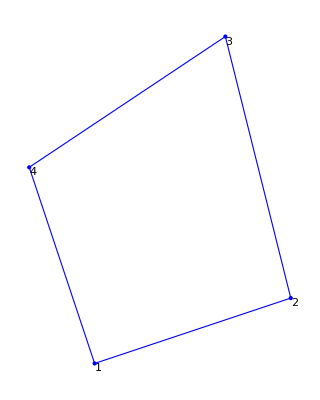

Length[nnodes] = 4

nels rows= 4

(0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0902343 | -0.115496 | -0.0160288 | 0.150145
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | -0.115496 | -0.277013 | 0.0834783 | -0.239883
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | 0.0518507 | 0.0812231 | -0.454073 | 0.13441
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.14789 | -0.182347 | 0.13441 | -0.182949
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | 0.316499 | 0.107979 | -0.278116 | -0.140373
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | 0.107979 | 0.4688 | -0.073706 | -0.00944048
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | -0.278116 | -0.073706 | 0.748217 | -0.144182
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.140373 | -0.00944048 | -0.144182 | 0.432273)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}}
topol={{1,2,3,4}}
eltype=1;
forcing=0.;
nnodes={{2,1},{5,2},{4,6},{1,4}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{kE,fE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixForm[kE]
```

{{{0,0},{0.5,0.5},{0.3,1}}}

{{1,2,3}}

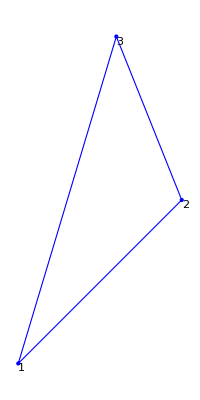

Length[nnodes] = 3

nels rows= 3

(0.40381 | 0.0952381 | -0.727619 | -0.0571429 | 0.32381 | -0.0380952
0.0952381 | 0.20381 | 0.00952381 | -0.194286 | -0.104762 | -0.00952381
-0.727619 | 0.00952381 | 1.57524 | -0.285714 | -0.847619 | 0.27619
-0.0571429 | -0.194286 | -0.285714 | 0.708571 | 0.342857 | -0.514286
0.32381 | -0.104762 | -0.847619 | 0.342857 | 0.52381 | -0.238095
-0.0380952 | -0.00952381 | 0.27619 | -0.514286 | -0.238095 | 0.52381)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{0.5,0.5},{0.3,1}}}
topol={{1,2,3}}
eltype=2;
forcing=0.;
nnodes={{0,0},{0.5,0.5},{0.3,1}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{kE,fE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixForm[kE]
```

{{{0,0},{10,0},{10,6},{0,6}}}

{{1,2,3,4}}

{{0,0},{10,0},{10,6},{0,6}}

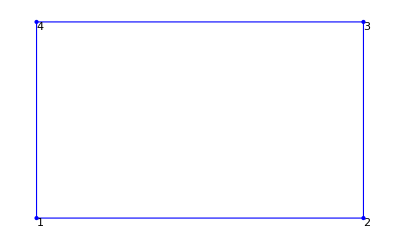

Length[nnodes] = 4

nels rows= 4

(4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

(4.33455×10^18 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^18 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^18 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^18 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

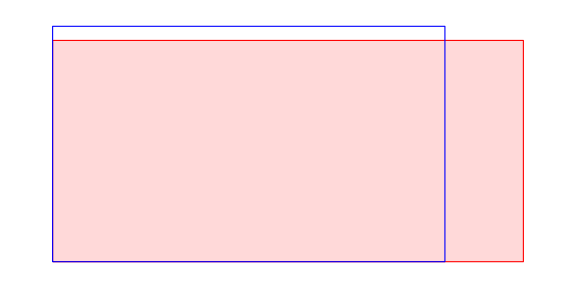

{0,0,0,0,0,0,0,0}

{0,0,0.002,0,0.002,-0.00036,0,-0.00036}

```mathematica
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{10,0},{10,6},{0,6}}}
topol={{1,2,3,4}}
eltype=1;
forcing=0.;
nnodes={{0,0},{10,0},{10,6},{0,6}}
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixForm[KE]
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{10^12,1},{1,1}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{6000,0}];
MatrixForm[KE]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
(KE.sol-FE)//Chop
sol//Chop
```

{{{0,0},{10,0},{0,6}},{{10,0},{10,6},{0,6}}}

{{1,2,3},{2,4,3}}

{{0,0},{10,0},{0,6},{10,6}}

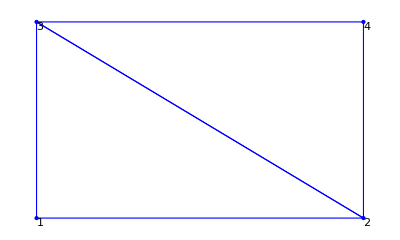

Length[nnodes] = 4

nels rows= 6

(6.50183×10^18 | 3.57143×10^6 | -3.2967×10^6 | -1.92308×10^6 | -3.20513×10^6 | -1.64835×10^6 | 0 | 0
3.57143×10^6 | 1.03114×10^19 | -1.64835×10^6 | -1.15385×10^6 | -1.92308×10^6 | -9.15751×10^6 | 0 | 0
-3.2967×10^6 | -1.64835×10^6 | 6.50183×10^6 | 0. | 0. | 3.57143×10^6 | -3.20513×10^6 | -1.92308×10^6
-1.92308×10^6 | -1.15385×10^6 | 0. | 1.03114×10^19 | 3.57143×10^6 | 0. | -1.64835×10^6 | -9.15751×10^6
-3.20513×10^6 | -1.92308×10^6 | 0. | 3.57143×10^6 | 6.50183×10^18 | 0. | -3.2967×10^6 | -1.64835×10^6
-1.64835×10^6 | -9.15751×10^6 | 3.57143×10^6 | 0. | 0. | 1.03114×10^7 | -1.92308×10^6 | -1.15385×10^6
0 | 0 | -3.20513×10^6 | -1.64835×10^6 | -3.2967×10^6 | -1.92308×10^6 | 6.50183×10^6 | 3.57143×10^6
0 | 0 | -1.92308×10^6 | -9.15751×10^6 | -1.64835×10^6 | -1.15385×10^6 | 3.57143×10^6 | 1.03114×10^7)

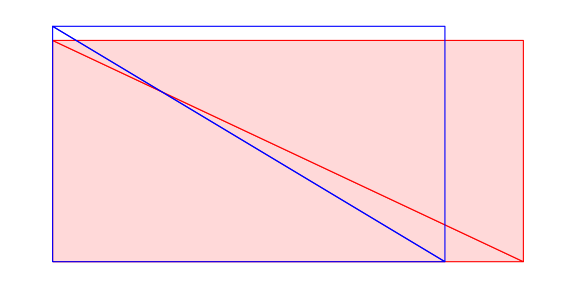

{0,0,0.002,0,0,-0.00036,0.002,-0.00036}

```mathematica
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{10,0},{0,6}},{{10,0},{10,6},{0,6}}}
topol={{1,2,3},{2,4,3}}
eltype=2;
forcing=0.;
nnodes={{0,0},{10,0},{0,6},{10,6}}
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,3,0,{{10^12,1},{1,1}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];
{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{6000,0}];
MatrixForm[KE]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
sol//Chop
```

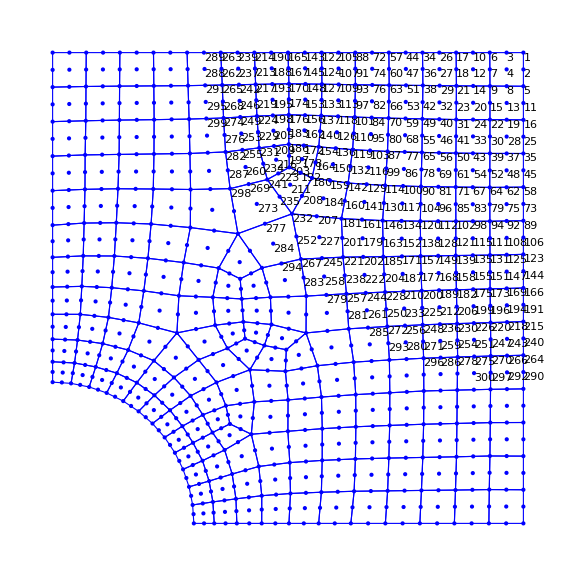

Length[nnodes] = 871

nels rows= 1818

-Graphics-

Possivel BUG!, Modificar rangesearch para o tamanho de elemento em uso!

rangesearch = 10.

5998.93

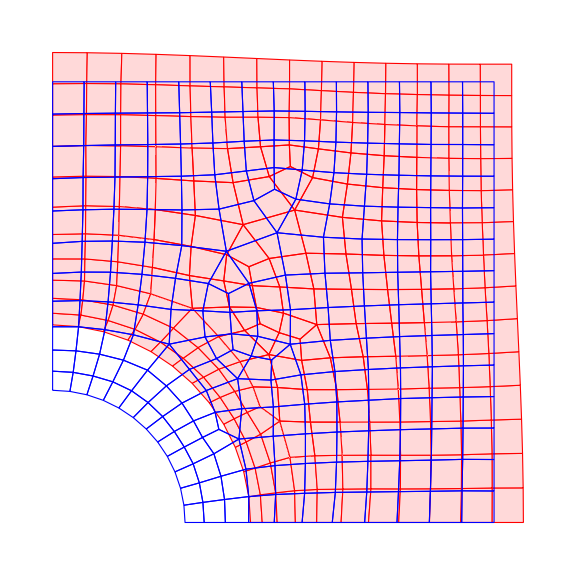

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elschapacomfuroleft.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\noschapacomfuroleft.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=2;
forcing=0.;
young=210000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=1;
(*AbsoluteTiming[Assemble[allcoords,topol,order,forcing,eltype];]*)
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,870,644,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,871,645,{{10^12,1},{1,1}},{0,0}];
tol=10^-4;
radius=300;
radiusdir=3;
coordy=0;(*naoprecisa*)
{newnodes,vecids}=ComputeBoundaryTopol[radiusdir,coordy,radius,nnodes,tol,order];
FE=Table[0,{Length[KE]}];
f[x_]:=10;
order=2;
FE=ContributeLineNewmanCurverd[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=7000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
AbsoluteTiming[ComputeSol[topol,nnodes,order,sol,eltype];]
```

{1.35937,Null}

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype];
stress=ComputeStress[(dsols),210000.,0.30][[1]];
```

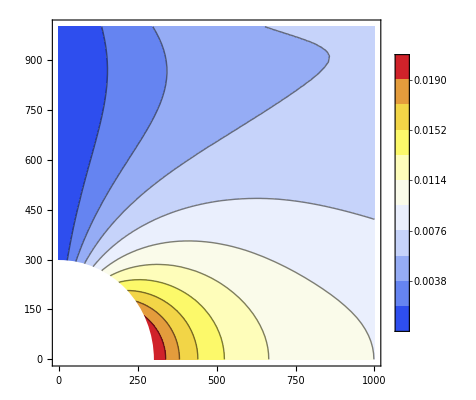

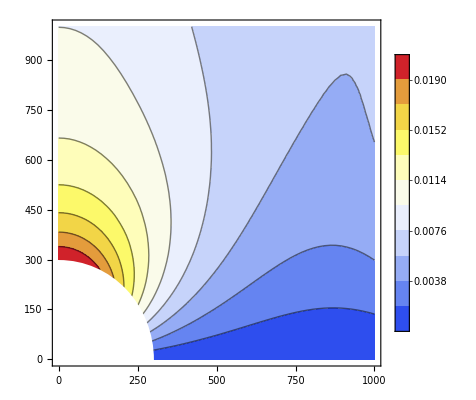

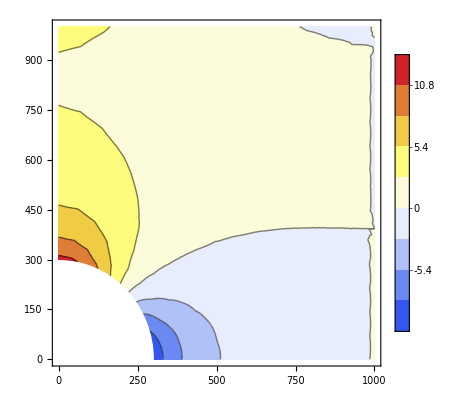

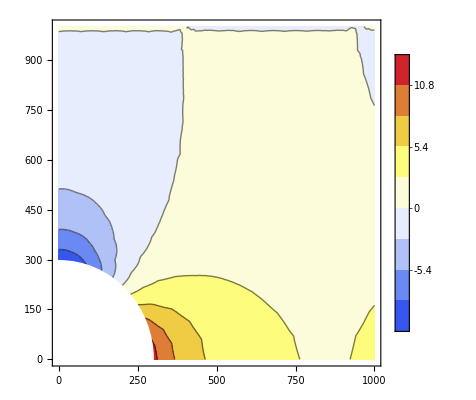

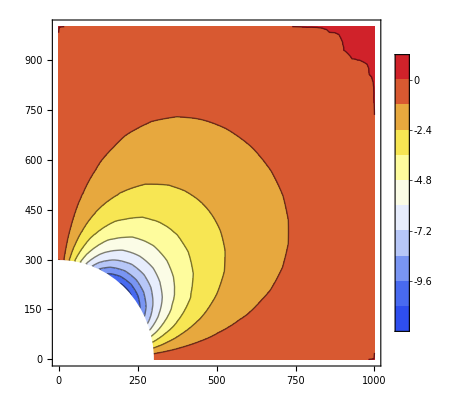

```mathematica
sollists={};
sx=1;
refine=0.5;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 


stresslists={};
sx=1;

For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->{-15,15}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->{-15,15}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10 ,PlotRange->{-12,2}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd]
```

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\FiniteElements\\elstrichapacomfurop2.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\FiniteElements\\nodestrichapacomfurop2.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,6}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=2;
forcing=0.;
young=210000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=2;
(*AbsoluteTiming[Assemble[allcoords,topol,order,forcing,eltype];]*)
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2000,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,4054,4927,{{10^12,1},{1,1}},{0,0}];
tol=10^-4;
radius=300;
radiusdir=3;
coordy=0;(*naoprecisa*)
{newnodes,vecids}=ComputeBoundaryTopol[radiusdir,coordy,radius,nnodes,tol,order];
FE=Table[0,{Length[KE]}];
f[x_]:=10;
order=2;
FE=ContributeLineNewmanCurverd[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=7000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
```